```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 312 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
(* SEE IF there's a g floating around that's missing *)
```

```mathematica
(* Figure out how to scale the constants m so that they drop out *)
```

```mathematica
(* Make the distinction between exact Lagrangian, verus the one they're using for an approximation *)
```

```mathematica
Clear[𝓇]
𝓇 = { R Sin[θ[t]] , R ( 1 - Cos[θ[t]] ) }
```

{R Sin[θ[t]],R (1-Cos[θ[t]])}

```mathematica
Series[ 𝓇 , { θ[t] , 0, 2 } ]
```

{R θ[t]+O[θ[t]]^3,1/2 R θ[t]^2+O[θ[t]]^3}

```mathematica
Normal[Series[ 𝓇 , { θ[t] , 0, 2 } ] ]
```

{R θ[t],1/2 R θ[t]^2}

```mathematica
Table [ x[i][t] , { i, 1,3 } ]
```

{x[1][t],x[2][t],x[3][t]}

```mathematica
Clear[q]
q = Table [ x[i][t] , { i, 1,3 } ]
```

{x[1][t],x[2][t],x[3][t]}

```mathematica
Clear[mass]
mass = { m , M , m }
```

{m,M,m}

```mathematica
Clear[r]
r = Table[√mass[[i]]  { R Sin[θ[i][t]] , R ( 1 - Cos[θ[i][t]] ) }  , { i, 1,3 }  ]
```

{{√m R Sin[θ[1][t]],√m R (1-Cos[θ[1][t]])},{√M R Sin[θ[2][t]],√M R (1-Cos[θ[2][t]])},{√m R Sin[θ[3][t]],√m R (1-Cos[θ[3][t]])}}

```mathematica
D[r, t] // MatrixForm
```

(√m R Cos[θ[1][t]] θ[1]'[t] | √m R Sin[θ[1][t]] θ[1]'[t]
√M R Cos[θ[2][t]] θ[2]'[t] | √M R Sin[θ[2][t]] θ[2]'[t]
√m R Cos[θ[3][t]] θ[3]'[t] | √m R Sin[θ[3][t]] θ[3]'[t])

```mathematica
Sum[ D[r[[i]], t]  . D[r[[i]], t]  , { i, 1, 3 } ]  // Expand  // Simplify
```

R^2 (m (θ[1]'[t])^2+M (θ[2]'[t])^2+m (θ[3]'[t])^2)

```mathematica
Clear[θReplace]
θReplace = 
Table[ θ[i][t]-> (x[i][t])/R , { i, 1, 3 } ]
```

{θ[1][t]→(x[1][t])/R,θ[2][t]→(x[2][t])/R,θ[3][t]→(x[3][t])/R}

```mathematica
D[θReplace, t]
```

{θ[1]'[t]→(x[1]'[t])/R,θ[2]'[t]→(x[2]'[t])/R,θ[3]'[t]→(x[3]'[t])/R}

```mathematica
Sum[ D[r[[i]], t]  . D[r[[i]], t]  , { i, 1, 3 } ] // Expand // Simplify
```

R^2 (m (θ[1]'[t])^2+M (θ[2]'[t])^2+m (θ[3]'[t])^2)

```mathematica
Sum[ D[r[[i]], t]  . D[r[[i]], t]  , { i, 1, 3 } ]   //. D[θReplace, t]  // Expand  // Simplify
```

m (x[1]'[t])^2+M (x[2]'[t])^2+m (x[3]'[t])^2

```mathematica
Clear[T]
T = 1/2 ( Sum[ D[r[[i]], t]  . D[r[[i]], t]  , { i, 1, 3 } ]   //. D[θReplace, t]  // Expand  // Simplify  )
```

1/2 (m (x[1]'[t])^2+M (x[2]'[t])^2+m (x[3]'[t])^2)

```mathematica
q
Differences[q] // TableForm
```

{x[1][t],x[2][t],x[3][t]}

-x[1][t]+x[2][t]
-x[2][t]+x[3][t]

```mathematica
Sum[(  Differences[q][[i]] )^2 , { i, 1, 2 } ]
```

(-x[1][t]+x[2][t])^2+(-x[2][t]+x[3][t])^2

```mathematica
Clear[V1]
V1 = 1/2 K ( Sum[(  Differences[q][[i]] )^2 , { i, 1, 2 } ]  )  ;
V1 // TraditionalForm
```

1/2 K ((x(2)(t)-x(1)(t))^2+(x(3)(t)-x(2)(t))^2)

```mathematica
r // MatrixForm
```

(√m R Sin[θ[1][t]] | √m R (1-Cos[θ[1][t]])
√M R Sin[θ[2][t]] | √M R (1-Cos[θ[2][t]])
√m R Sin[θ[3][t]] | √m R (1-Cos[θ[3][t]]))

```mathematica
r[[1,2]]
r[[2,2]]
r[[3,2]]
```

√m R (1-Cos[θ[1][t]])

√M R (1-Cos[θ[2][t]])

√m R (1-Cos[θ[3][t]])

```mathematica
Table[ r[[i,2]] , { i, 1, 3 } ]  // MatrixForm
```

(√m R (1-Cos[θ[1][t]])
√M R (1-Cos[θ[2][t]])
√m R (1-Cos[θ[3][t]]))

```mathematica
Sum[ √mass[[i]] r[[i,2]] , { i, 1, 3 } ]
```

m R (1-Cos[θ[1][t]])+M R (1-Cos[θ[2][t]])+m R (1-Cos[θ[3][t]])

```mathematica
Sum[ √mass[[i]] r[[i,2]] , { i, 1, 3 } ]  
 Sum[ √mass[[i]] r[[i,2]] , { i, 1, 3 } ]    /. θReplace
```

m R (1-Cos[θ[1][t]])+M R (1-Cos[θ[2][t]])+m R (1-Cos[θ[3][t]])

m R (1-Cos[(x[1][t])/R])+M R (1-Cos[(x[2][t])/R])+m R (1-Cos[(x[3][t])/R])

```mathematica
Clear[V2]
V2 =  Sum[ √mass[[i]] r[[i,2]] , { i, 1, 3 } ]    /. θReplace
```

m R (1-Cos[(x[1][t])/R])+M R (1-Cos[(x[2][t])/R])+m R (1-Cos[(x[3][t])/R])

```mathematica
Clear[V]
V = V1 + V2  ;
V // pdConv
```

1/2 K ((x(2)(t)-x(1)(t))^2+(x(3)(t)-x(2)(t))^2)+m R (1-cos((x(1)(t))/R))+m R (1-cos((x(3)(t))/R))+M R (1-cos((x(2)(t))/R))

```mathematica
Clear[ℒ]
ℒ = T - V  ;
ℒ // TraditionalForm
```

-1/2 K ((x(2)(t)-x(1)(t))^2+(x(3)(t)-x(2)(t))^2)+1/2 (m (x(1)'(t))^2+m (x(3)'(t))^2+M (x(2)'(t))^2)-m R (1-cos((x(1)(t))/R))-m R (1-cos((x(3)(t))/R))-M R (1-cos((x(2)(t))/R))

```mathematica
q
```

{x[1][t],x[2][t],x[3][t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ] 
D[ D[ ℒ , D[q[[3]], t] ] , t ] - D[ ℒ , q[[3]] ]
```

m Sin[(x[1][t])/R]-K (-x[1][t]+x[2][t])+m x[1]''[t]

M Sin[(x[2][t])/R]+1/2 K (2 (-x[1][t]+x[2][t])-2 (-x[2][t]+x[3][t]))+M x[2]''[t]

m Sin[(x[3][t])/R]+K (-x[2][t]+x[3][t])+m x[3]''[t]

```mathematica
Table[ 
D[ D[ ℒ , D[q[[i]], t] ] , t ] - D[ ℒ , q[[i]] ] == 0 , 
{ i, 1, 3 } ]  // Simplify // TableForm
```

K x[1][t]+m (Sin[(x[1][t])/R]+x[1]''[t])==K x[2][t]
2 K x[2][t]+M (Sin[(x[2][t])/R]+x[2]''[t])==K (x[1][t]+x[3][t])
K x[2][t]==K x[3][t]+m (Sin[(x[3][t])/R]+x[3]''[t])

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-K x[1][t]+K x[2][t]-m (Sin[(x[1][t])/R]+x[1]''[t])==0
-M Sin[(x[2][t])/R]+K x[1][t]-2 K x[2][t]+K x[3][t]-M x[2]''[t]==0
K x[2][t]-K x[3][t]-m (Sin[(x[3][t])/R]+x[3]''[t])==0

```mathematica
Clear[parameters]
parameters = { 
K-> 300 , 
m-> 5 , 
M -> 13 , 
R-> 5 , 
g-> 9.8  
} ;
parameters // TableForm
```

K→300
m→5
M→13
R→5
g→9.8

```mathematica
eqs /. parameters  // Expand // TableForm
```

-5 Sin[1/5 x[1][t]]-300 x[1][t]+300 x[2][t]-5 x[1]''[t]==0
-13 Sin[1/5 x[2][t]]+300 x[1][t]-600 x[2][t]+300 x[3][t]-13 x[2]''[t]==0
-5 Sin[1/5 x[3][t]]+300 x[2][t]-300 x[3][t]-5 x[3]''[t]==0

```mathematica
Clear[ics]
ics = { 
x[1][0] == 0.1 ,
x[1]'[0] == 0 , 
x[2][0] == 0.2 , 
x[2]'[0] == 0  , 
x[3][0] == 0.3 , 
x[3]'[0] == 0 
} ;
ics // TableForm
```

x[1][0]==0.1
x[1]'[0]==0
x[2][0]==0.2
x[2]'[0]==0
x[3][0]==0.3
x[3]'[0]==0

```mathematica
Clear[solution]
solution[t_] = First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 300 } ] ]
```

{x[1][t]→InterpolatingFunction[…][t],x[2][t]→InterpolatingFunction[…][t],x[3][t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t]] , { t, 0, 10 } , PlotLabels-> q  ]
```

-Graphics-

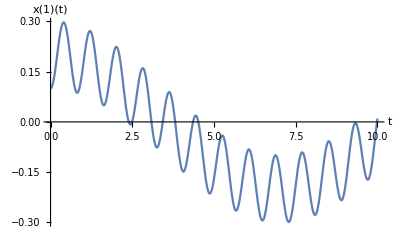

```mathematica
Plot[ q[[1]] /. solution [t], { t, 0, 10 } , AxesLabel-> { t, q[[1]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,75 , 0.5  } ]
```

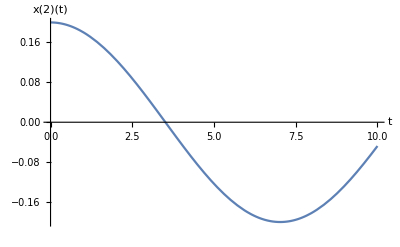

```mathematica
Plot[ q[[2]] /. solution[t] , { t, 0, 10 } , AxesLabel-> { t, q[[2]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 1 ,75 , 0.5  } ]
```

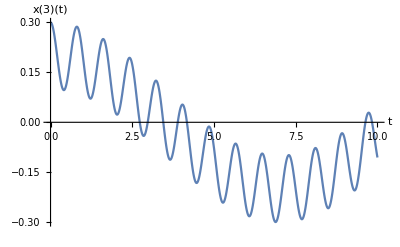

```mathematica
Plot[ q[[3]] /. solution[t] , { t, 0, 10 } , AxesLabel-> { t, q[[3]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[3,2]] , solution'[t][[3,2]] } , { t , 0, tmax } , AxesLabel-> { q[[3]] , D[q[[3]], t] } ]  ,
{ tmax , 1 ,75 , 0.5  } ]
```

```mathematica
r // MatrixForm
```

(√m R Sin[θ[1][t]] | √m R (1-Cos[θ[1][t]])
√M R Sin[θ[2][t]] | √M R (1-Cos[θ[2][t]])
√m R Sin[θ[3][t]] | √m R (1-Cos[θ[3][t]]))

```mathematica
Normal[Series[ r[[1]] , { θ[1][t] , 0 , 2 } ] ]
```

{√m R θ[1][t],1/2 √m R (θ[1][t])^2}

```mathematica
Table[
Normal[Series[ r[[i]] , { θ[i][t] , 0 , 2 } ] ] , { i, 1, 3 } ]  // MatrixForm
```

(√m R θ[1][t] | 1/2 √m R (θ[1][t])^2
√M R θ[2][t] | 1/2 √M R (θ[2][t])^2
√m R θ[3][t] | 1/2 √m R (θ[3][t])^2)

```mathematica
Clear[rLinearized]
rLinearized = 
Table[Normal[Series[ r[[i]] , { θ[i][t] , 0 , 2 } ] ] , { i, 1, 3 } ] ;
rLinearized // MatrixForm
```

(√m R θ[1][t] | 1/2 √m R (θ[1][t])^2
√M R θ[2][t] | 1/2 √M R (θ[2][t])^2
√m R θ[3][t] | 1/2 √m R (θ[3][t])^2)

```mathematica
θReplace
```

{θ[1][t]→(x[1][t])/R,θ[2][t]→(x[2][t])/R,θ[3][t]→(x[3][t])/R}

```mathematica
rLinearized /. θReplace  // MatrixForm
```

(√m x[1][t] | (√m (x[1][t])^2)/(2 R)
√M x[2][t] | (√M (x[2][t])^2)/(2 R)
√m x[3][t] | (√m (x[3][t])^2)/(2 R))

```mathematica
Clear[V2linearized]
Sum[ √mass[[i]]  g rLinearized[[i,2]] , { i, 1, 3 } ] 
V2linearized = Sum[ √mass[[i]]  g rLinearized[[i,2]] , { i, 1, 3 } ]  /. θReplace
```

1/2 g m R (θ[1][t])^2+1/2 g M R (θ[2][t])^2+1/2 g m R (θ[3][t])^2

(g m (x[1][t])^2)/(2 R)+(g M (x[2][t])^2)/(2 R)+(g m (x[3][t])^2)/(2 R)

```mathematica
V1 // Expand
```

1/2 K (x[1][t])^2-K x[1][t] x[2][t]+K (x[2][t])^2-K x[2][t] x[3][t]+1/2 K (x[3][t])^2

```mathematica
T
V1 // Expand 
V2linearized
```

1/2 (m (x[1]'[t])^2+M (x[2]'[t])^2+m (x[3]'[t])^2)

1/2 K (x[1][t])^2-K x[1][t] x[2][t]+K (x[2][t])^2-K x[2][t] x[3][t]+1/2 K (x[3][t])^2

(g m (x[1][t])^2)/(2 R)+(g M (x[2][t])^2)/(2 R)+(g m (x[3][t])^2)/(2 R)

```mathematica
T + V1 + V2linearized  // Expand  // Simplify  // Expand // pdConv
```

(g m (x(1)(t))^2)/(2 R)+(g m (x(3)(t))^2)/(2 R)+(g M (x(2)(t))^2)/(2 R)+1/2 K (x(1)(t))^2+K (x(2)(t))^2+1/2 K (x(3)(t))^2-K x(1)(t) x(2)(t)-K x(2)(t) x(3)(t)+1/2 m ((∂x(1)(t))/(∂t))^2+1/2 m ((∂x(3)(t))/(∂t))^2+1/2 M ((∂x(2)(t))/(∂t))^2

```mathematica
Clear[ℒlinearized]
ℒlinearized = 
T - V1 - V2linearized  // Expand  // Simplify  // Expand  ;
ℒlinearized // pdConv
```

-(g m (x(1)(t))^2)/(2 R)-(g m (x(3)(t))^2)/(2 R)-(g M (x(2)(t))^2)/(2 R)-1/2 K (x(1)(t))^2-K (x(2)(t))^2-1/2 K (x(3)(t))^2+K x(1)(t) x(2)(t)+K x(2)(t) x(3)(t)+1/2 m ((∂x(1)(t))/(∂t))^2+1/2 m ((∂x(3)(t))/(∂t))^2+1/2 M ((∂x(2)(t))/(∂t))^2

```mathematica
D[ D[ ℒlinearized , D[q[[1]], t] ], t ]  - D[ ℒlinearized , q[[1]] ] // Simplify 
D[ D[ ℒlinearized , D[q[[2]], t] ], t ]  - D[ ℒlinearized , q[[2]] ] // Simplify 
D[ D[ ℒlinearized , D[q[[3]], t] ], t ]  - D[ ℒlinearized , q[[3]] ] // Simplify
```

(K+(g m)/R) x[1][t]-K x[2][t]+m x[1]''[t]

-K x[1][t]+(2 K+(g M)/R) x[2][t]-K x[3][t]+M x[2]''[t]

-K x[2][t]+(K+(g m)/R) x[3][t]+m x[3]''[t]

```mathematica
Table[
D[ D[ ℒlinearized , D[q[[i]], t] ], t ]  - D[ ℒlinearized , q[[i]] ] == 0 , 
{ i, 1, 3 } ]  // Simplify // TableForm
```

(K+(g m)/R) x[1][t]+m x[1]''[t]==K x[2][t]
(2 K+(g M)/R) x[2][t]+M x[2]''[t]==K (x[1][t]+x[3][t])
(K+(g m)/R) x[3][t]+m x[3]''[t]==K x[2][t]

```mathematica
Clear[eqsLinearized]
eqsLinearized = 
EulerEquations[ ℒlinearized , q , t ] ; 
eqsLinearized // TableForm
```

-((g m+K R) x[1][t])/R+K x[2][t]-m x[1]''[t]==0
K x[1][t]-((g M+2 K R) x[2][t])/R+K x[3][t]-M x[2]''[t]==0
K x[2][t]-((g m+K R) x[3][t])/R-m x[3]''[t]==0

```mathematica
Clear[solutionLinearized]
solutionLinearized = 
NDSolve[ Union[ eqsLinearized /. parameters , ics ] , q , { t, 0, 10 } ]
```

{{x[1][t]→InterpolatingFunction[…][t],x[2][t]→InterpolatingFunction[…][t],x[3][t]→InterpolatingFunction[…][t]}}

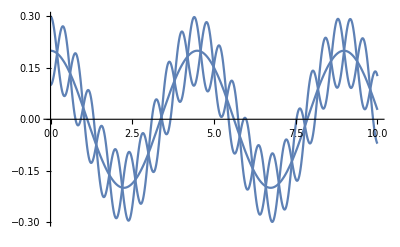

```mathematica
Plot[ q /. solutionLinearized , { t, 0, 10} ]
```

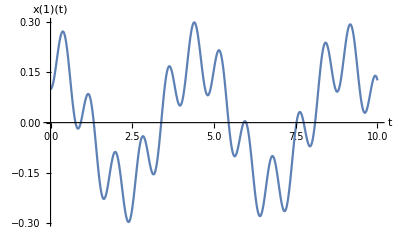

```mathematica
Plot[ q[[1]] /. solutionLinearized , { t, 0, 10} , AxesLabel-> { t, q[[1]] }  ]
```

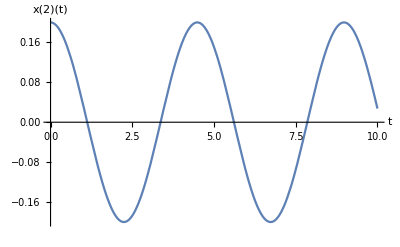

```mathematica
Plot[ q[[2]] /. solutionLinearized , { t, 0, 10} , AxesLabel-> { t, q[[2]] }  ]
```

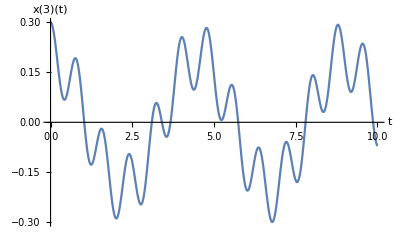

```mathematica
Plot[ q[[3]] /. solutionLinearized , { t, 0, 10} , AxesLabel-> { t, q[[3]] }  ]
```

```mathematica
eqsLinearized // TableForm
```

-((g m+K R) x[1][t])/R+K x[2][t]-m x[1]''[t]==0
K x[1][t]-((g M+2 K R) x[2][t])/R+K x[3][t]-M x[2]''[t]==0
K x[2][t]-((g m+K R) x[3][t])/R-m x[3]''[t]==0

```mathematica
Clear[𝒜]
𝒜 = Table[ A[i] , { i, 1, 3 } ]
```

{A[1],A[2],A[3]}

```mathematica
Table[ 𝒜[[i]] Exp[ ⅈ ω ]  , { i, 1, 3 } ]
```

{ⅇ^(ⅈ ω) A[1],ⅇ^(ⅈ ω) A[2],ⅇ^(ⅈ ω) A[3]}

```mathematica
Clear[trial]
trial = 
Table[x[i][t] -> 𝒜[[i]] Exp[ ⅈ ω  t] , { i, 1 , 3 } ]  ;
trial // TableForm
```

x[1][t]→ⅇ^(ⅈ t ω) A[1]
x[2][t]→ⅇ^(ⅈ t ω) A[2]
x[3][t]→ⅇ^(ⅈ t ω) A[3]

```mathematica
D[trial, t] // TableForm
```

x[1]'[t]→ⅈ ⅇ^(ⅈ t ω) ω A[1]
x[2]'[t]→ⅈ ⅇ^(ⅈ t ω) ω A[2]
x[3]'[t]→ⅈ ⅇ^(ⅈ t ω) ω A[3]

```mathematica
D[D[trial, t], t] // TableForm
```

x[1]''[t]→-ⅇ^(ⅈ t ω) ω^2 A[1]
x[2]''[t]→-ⅇ^(ⅈ t ω) ω^2 A[2]
x[3]''[t]→-ⅇ^(ⅈ t ω) ω^2 A[3]

```mathematica
eqsLinearized // TableForm
```

-((g m+K R) x[1][t])/R+K x[2][t]-m x[1]''[t]==0
K x[1][t]-((g M+2 K R) x[2][t])/R+K x[3][t]-M x[2]''[t]==0
K x[2][t]-((g m+K R) x[3][t])/R-m x[3]''[t]==0

```mathematica
eqsLinearized /. trial /. D[D[trial, t], t]  // Expand  //Simplify //  TableForm
```

(ⅇ^(ⅈ t ω) (-g m A[1]+m R ω^2 A[1]+K R (-A[1]+A[2])))/R==0
(ⅇ^(ⅈ t ω) (M (-g+R ω^2) A[2]+K R (A[1]-2 A[2]+A[3])))/R==0
(ⅇ^(ⅈ t ω) (K R (A[2]-A[3])+m (-g+R ω^2) A[3]))/R==0

```mathematica
Clear[eq1]
eq1 = 
Assuming[ Exp[ ⅈ ω t ] ≠ 0 ,   DivideSides[  eqsLinearized /. trial /. D[D[trial, t], t]   , Exp[ ⅈ ω t  ]]] // Expand
```

{-K A[1]-(g m A[1])/R+m ω^2 A[1]+K A[2]==0,K A[1]-2 K A[2]-(g M A[2])/R+M ω^2 A[2]+K A[3]==0,K A[2]-K A[3]-(g m A[3])/R+m ω^2 A[3]==0}

```mathematica
eq1 // TableForm
```

-K A[1]-(g m A[1])/R+m ω^2 A[1]+K A[2]==0
K A[1]-2 K A[2]-(g M A[2])/R+M ω^2 A[2]+K A[3]==0
K A[2]-K A[3]-(g m A[3])/R+m ω^2 A[3]==0

```mathematica
𝒜
```

{A[1],A[2],A[3]}

```mathematica
Coefficient[ eq1[[1,1]] , 𝒜 ] 
Coefficient [ eq1[[2,1]] , 𝒜  ]  
Coefficient[ eq1[[3,1]] , 𝒜  ]
```

{-K-(g m)/R+m ω^2,K,0}

{K,-2 K-(g M)/R+M ω^2,K}

{0,K,-K-(g m)/R+m ω^2}

```mathematica
Clear[secular]
secular = 
Table[Coefficient[ eq1[[i,1]] , 𝒜 ] , { i, 1, 3 } ]  ;
secular // MatrixForm
```

(-K-(g m)/R+m ω^2 | K | 0
K | -2 K-(g M)/R+M ω^2 | K
0 | K | -K-(g m)/R+m ω^2)

```mathematica
Det[ secular ]
```

-K (-K^2-(g K m)/R+K m ω^2)+(-K-(g m)/R+m ω^2) (-K^2+(-K-(g m)/R+m ω^2) (-2 K-(g M)/R+M ω^2))

```mathematica
(* Check this carefully, they only have two distinct, one repeated , you've got three *)
```

```mathematica
Solve[ Det[ secular ]  == 0 , ω ]
```

{{ω→-(√g)/(√R)},{ω→(√g)/(√R)},{ω→-(√(g m+K R))/(√m √R)},{ω→(√(g m+K R))/(√m √R)},{ω→-(√(g m M+2 K m R+K M R))/(√m √M √R)},{ω→(√(g m M+2 K m R+K M R))/(√m √M √R)}}

```mathematica
Clear[ω1]
ω1 = 
Solve[ Det[ secular ]  == 0 , ω ] [[4]]
```

{ω→(√(g m+K R))/(√m √R)}

```mathematica
Clear[ω2]
ω2 = 
Solve[ Det[ secular ]  == 0 , ω ] [[6]]
```

{ω→(√(g m M+2 K m R+K M R))/(√m √M √R)}